# Voronoi Cells in Metric Algebraic Geometry of Plane Curves

```mathematica
butterfly[x_,y_]:=x^4-x^2y^2+y^4-4x^2-2y^2-x-4y+1
```

### Other Curves:

```mathematica
trott[x_,y_]:=144(x^4+y^4)-225(x^2+y^2)+350x^2y^2+81
```

```mathematica
cardiod[x_,y_]:=(x^2+y^2+x)^2-(x^2+y^2)
```

```mathematica
ellipse[x_,y_]:=(x/2)^2+(y)^2-1
```

```mathematica
elliptic[x_,y_]:=y^2-x(x-2)(x+1)
```

```mathematica
circle[x_,y_]:=x^2+y^2-1
```

```mathematica
deltoid[x_,y_]:=-27+8 x (x^2-3 y^2)+18 (x^2+y^2)+(x^2+y^2)^2
```

### Set f = your favorite curve, then evaluate the whole notebook. This may take a few minutes to finish.

```mathematica
f =butterfly;
```

## Hidden code

```mathematica
h[f_,x_,y_]:=-(D[f[x,y],y])^2 D[f[x,y],x,x] + 2 D[f[x,y],x]D[f[x,y],y]D[f[x,y],x,y]-(D[f[x,y],x])^2 D[f[x,y],y,y]
g[f_,x_,y_]:=(D[f[x,y],x])^2+(D[f[x,y],y])^2
s[f_,{x_,y_}]:=h[f,x,y]/g[f,x,y]^(3/2)
```

```mathematica
crit[f_,x_,y_]:=Det[{g[f,x,y]Grad[h[f,x,y],{x,y}]-3/2 h[f,x,y]Grad[g[f,x,y],{x,y}],Grad[f[x,y],{x,y}]}]
```

```mathematica
RealSols=NSolve[{crit[f,x,y]==0,f[x,y]==0},{x,y},Reals]
```

{{x→2.81101,y→2.73643},{x→-2.67611,y→2.61651},{x→2.23616,y→-2.02777},{x→2.02184,y→-0.306121},{x→-1.86218,y→-1.60919},{x→-0.062367,y→1.94515},{x→1.37011,y→-1.73717},{x→-1.63834,y→-0.483685},{x→0.977245,y→-1.26352},{x→-1.09551,y→-0.501745},{x→-0.0742129,y→0.235922}}

```mathematica
points=Table[{RealSols[[i,1,2]],RealSols[[i,2,2]]},{i,1,Length[RealSols]}]
```

{{2.81101,2.73643},{-2.67611,2.61651},{2.23616,-2.02777},{2.02184,-0.306121},{-1.86218,-1.60919},{-0.062367,1.94515},{1.37011,-1.73717},{-1.63834,-0.483685},{0.977245,-1.26352},{-1.09551,-0.501745},{-0.0742129,0.235922}}

```mathematica
mylistreals=NSolve[{f[x1,y1]==0,f[x2,y2]==0,D[f[x1,y1],x1](y1-y2)==D[f[x1,y1],y1](x1-x2),D[f[x2,y2],x2](y1-y2)==D[f[x2,y2],y2](x1-x2)},{x1,y1,x2,y2},Reals];
dual[vertices_]:=Module[{rstatic,randeq,eqset,vertexcandidates,vertex,poly,liftedv,maxheight},
liftedv=Table[{vertices[[i,1]],vertices[[i,2]],vertices[[i,1]]^2+vertices[[i,2]]^2},{i,1,Length[vertices]}];
maxheight=Max[Table[vertices[[i,1]]^2+vertices[[i,2]]^2,{i,1,Length[vertices]}]];
rstatic=Append[Table[z≥ liftedv[[i,3]]+2liftedv[[i,1]](x-liftedv[[i,1]])+2liftedv[[i,2]](y-liftedv[[i,2]]),{i,1,Length[liftedv]}],z≤1.5maxheight];
randeq=Append[Table[z== liftedv[[i,3]]+2liftedv[[i,1]](x-liftedv[[i,1]])+2liftedv[[i,2]](y-liftedv[[i,2]]),{i,1,Length[liftedv]}],z==1.3maxheight];
eqset=Subsets[randeq,{3}];
vertexcandidates=Flatten[Table[Solve[eqset[[i]]],{i,Length[eqset]}],1];
vertex=Union[Select[vertexcandidates,
And[Not[MemberQ[rstatic/.#,False]],Length[#]==3]&
]];
poly=Table[{vertex[[1,1,2]],vertex[[1,2,2]],vertex[[1,3,2]]},{i,1,Length[vertex]}];
ConvexHullMesh[Table[{vertex[[i,1,2]],vertex[[i,2,2]],vertex[[i,3,2]]},{i,1,Length[vertex]}],ViewPoint->{0,0,-1},MeshCellStyle->{{1}->{Red,Opacity[0]}}]
]
```

```mathematica
dualpair[vertices_]:={ConvexHullMesh[Table[{vertices[[i,1]],vertices[[i,2]],vertices[[i,1]]^2+vertices[[i,2]]^2},{i,1,Length[vertices]}],ViewPoint->{0,0,-1},MeshCellStyle->{{1}->{Red,Opacity[0]}}],dual[vertices]}
```

```mathematica
ShorePts[f_,n_]:=Module[{shpts,shore},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n];
shpts=RandomSample[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1],n];
Return[shpts]
]
```

```mathematica
sings[f_]:=NSolve[{D[f[x,y],x]==0,D[f[x,y],y]==0,f[x,y]==0},{x,y}]
```

```mathematica
MakeVoronoi[f_,n_]:=Module[{shpts,shore,k,sing},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n,Frame->False];
k=Length[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
sing=sings[f];
shpts=Join[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1],Table[{sing[[i,1,2]],sing[[i,2,2]]},{i,1,Length[sing]}]];
Print[k];
Show[shore,VoronoiMesh[shpts,{{-5,5},{-5,5}},
PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Blue,Thickness[0.0015]}}],Graphics[{Green,PointSize[0.005],Point[shpts]}]]
]
```

```mathematica
MakeDelaunay[f_,n_]:=Module[{shpts,shore,k},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n,Frame->False];
k=Length[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
shpts=Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1];
Print[k];
Show[shore,DelaunayMesh[shpts,{{-4,4},{-4,4}},PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Red,Thickness[0.0015]}}],Graphics[{Green,PointSize[0.005],Point[shpts]}]]
]
```

```mathematica
LongEdgeQ[f_,e_]:=Module[{candidates,intersecs},candidates=NSolve[{f[x,y]==0,(e[[1,2]]-e[[2,2]])(e[[1,1]]-x)==(e[[1,2]]-y)(e[[1,1]]-e[[2,1]])},{x,y},Reals];
intersecs=Table[RegionIntersection[Line[e],Line[{{candidates[[i,1,2]],candidates[[i,2,2]]}-{1,1},{candidates[[i,1,2]],candidates[[i,2,2]]}+{1,1}}]],{i,1,Length[candidates]}];
If[Count[intersecs,EmptyRegion[2]]<Length[intersecs],True,False]
]
```

```mathematica
MedialAxis[f_,n_]:=Module[{shpts,shore,k,vor,cells,cellcoord,newlength,i,Poly,minlength,Polycoords,polyedges,medialedges,minedge,edges,edgecoord},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n];
k=Length[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
Print[k];
shpts=DeleteDuplicates[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
vor=VoronoiMesh[shpts,PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Blue,Thickness[0.0015]}}];
cells=MeshCells[vor,2];
cellcoord=Table[First@Map[MeshCoordinates[vor][[#]]&,cells,{2}][[i]],{i,1,Length[cells]}];
edges=MeshCells[vor,1];
edgecoord=Table[First@Map[MeshCoordinates[vor][[#]]&,edges,{2}][[i]],{i,1,Length[edges]}];
medialedges={};
For[i = 1, i≤ Length[cells],i++,
Poly=cellcoord[[i]];
polyedges=Select[edgecoord,SubsetQ[Poly,#]&];
For[k=1,k≤Length[polyedges],k++,If[LongEdgeQ[f,polyedges[[k]]]==False,medialedges=Join[medialedges,{ polyedges[[k]]}]];
];
];
(*Show[ContourPlot[tooth[x,y]==0,{x,-3,3},{y,-3,3},Axes->False,Frame->False,ContourStyle->Purple],VoronoiMesh[shpts,{{-4,4},{-4,4}},
PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Blue,Thickness[0.0015]}}],Graphics[{Red,Line[medialedges],Red,PointSize[0.01],Point[shpts]}]],*)Show[ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},Axes->False,Frame->False,ContourStyle->Purple],Graphics[{Red,Line[medialedges]}]]
]
```

```mathematica
ApproxBottlenecks[f_,n_]:=Module[{shpts,shore,point,edge,cell,k,vor,cells,cellcoord,newlength,i,Poly,minlength,Polycoords,polyedges,medialedges,minedge,edges,annoyinglist,edgecoord,thecells,bottlenecks,cellpositions,lengths},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n];
k=Length[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
Print[k];
shpts=DeleteDuplicates[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
vor=VoronoiMesh[shpts,PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Blue,Thickness[0.0015]}}];
cell=MeshCells[vor,2];
cells=Table[MeshCells[vor,2][[i,1]],{i,1,Length[MeshCells[vor,2]]}];
cellcoord=Table[First@Map[MeshCoordinates[vor][[#]]&,cell,{2}][[i]],{i,1,Length[cells]}];
edge=MeshCells[vor,1];
edges=Table[MeshCells[vor,1][[i,1]],{i,1,Length[MeshCells[vor,1]]}];
edgecoord=Table[First@Map[MeshCoordinates[vor][[#]]&,edge,{2}][[i]],{i,1,Length[edges]}];
annoyinglist=Sort[Region`Mesh`MeshNearestCellIndex[vor,#]->#&/@shpts];
medialedges={};
bottlenecks={};
lengths={};
For[i = 1, i≤ Length[cells],i++,
Poly=cellcoord[[i]];
polyedges=Select[edgecoord,SubsetQ[Poly,#]&];
For[k=1,k≤Length[polyedges],k++,
If[LongEdgeQ[f,polyedges[[k]]]==False,
thecells=Select[cellcoord,SubsetQ[#,polyedges[[k]]]&];
cellpositions=Flatten[Table[Position[cellcoord,thecells[[i]]],{i,1,Length[thecells]}]];
If[Length[cellpositions]==2,
If[Length[RegionIntersection[Line[polyedges[[k]]],Line[{annoyinglist[[cellpositions[[1]],2]],annoyinglist[[cellpositions[[2]],2]]}]][[1]]]==1
,
medialedges=Join[medialedges,{ polyedges[[k]]}];
bottlenecks=Join[bottlenecks,{Line[{annoyinglist[[cellpositions[[1]],2]],annoyinglist[[cellpositions[[2]],2]]}]}];
lengths=Join[lengths,{EuclideanDistance[annoyinglist[[cellpositions[[1]],2]],annoyinglist[[cellpositions[[2]],2]]]}]]
]];
];
];
Print[(Min[lengths]/2)//N];
Show[ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},Axes->False,Frame->False,ContourStyle->Purple],VoronoiMesh[shpts,{{-4,4},{-4,4}},
PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Lighter[Lighter[Lighter[Blue]]],Thickness[0.001]}}],Graphics[{Red,Line[medialedges],Red,PointSize[0.01],Point[shpts],Thickness[0.003],Darker[Green],bottlenecks}]]
]
```

```mathematica
circumcenter[{p1_,p2_,p3_}]:=Module[{ax,ay,bx,by,cx,cy,a,b,c,d,e,f,g,centerx,centery,r},{ax,ay}=p1;
{bx,by}=p2;
{cx,cy}=p3;
a=bx-ax;
b=by-ay;
c=cx-ax;
d=cy-ay;
e=a (ax+bx)+b (ay+by);
f=c (ax+cx)+d (ay+cy);
g=2 (a (cy-by)-b (cx-bx));
If[g==0,False,{centerx=(d e-b f)/g,centery=(a f-c e)/g,r=Sqrt[(ax-centerx)^2+(ay-centery)^2]}];
{centerx,centery}]
```

```mathematica
MedialAxisDelaunay[f_,n_]:=Module[{shpts,shore,k,del,cells,cellcoord,i,medialpoints},
shore=ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},PlotPoints->n,MaxRecursion->4];
(*k=Length[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
Print[k];*)
shpts=DeleteDuplicates[Flatten[Cases[Normal@shore,Line[x_]:>x,Infinity],1]];
del=DelaunayMesh[shpts,PlotTheme->"Lines",MeshCellStyle->{{1,All}->{Red,Thickness[0.0015]}}];
cells=MeshCells[del,2];
cellcoord=Table[First@Map[MeshCoordinates[del][[#]]&,cells,{2}][[i]],{i,1,Length[cells]}];
medialpoints=Table[circumcenter[cellcoord[[i]]],{i,1,Length[cells]}];
Print[Length[shpts]];
Show[ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},Axes->False,Frame->False,ContourStyle->Purple],Graphics[{Red,Point[medialpoints]}]]
]
```

```mathematica
BottleneckPicture[f_]:=Show[ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3},ContourStyle->Purple,Frame->False],Graphics[
Flatten[Table[
{Lighter[Lighter[Blue]], Line[{{mylistreals[[i,1,2]],mylistreals[[i,2,2]]},{mylistreals[[i,3,2]],mylistreals[[i,4,2]]}}],Red,PointSize[0.01],Point[{{mylistreals[[i,1,2]],mylistreals[[i,2,2]]},{mylistreals[[i,3,2]],mylistreals[[i,4,2]]}}]},{i,1,Length[mylistreals]}]]
]]
```

```mathematica
smallestbottleneck=Min[Table[EuclideanDistance[{mylistreals[[i,1,2]],mylistreals[[i,2,2]]},{mylistreals[[i,3,2]],mylistreals[[i,4,2]]}],{i,1,Length[mylistreals]}]];
```

```mathematica
critCurvaturePlot[f_]:=Show[ContourPlot[{f[x,y]==0},{x,-3,3},{y,-3,3},Axes->False,Frame->False,ContourStyle->Purple],Graphics[{Red,PointSize[0.015],Point[points]}]]
```

```mathematica
maxlcurvature=Max[Table[Abs[s[f,{x,y}]]/.{x->points[[i,1]],y->points[[i,2]]},{i,1,Length[points]}]];
```

## Outputs

### In most of the commands there is a second argument which is an integer. This roughly correlates with how many points should be sampled from the curve. If the integer is too small, sometimes there will be errors. The printed numbers are how many points were sampled.

## Voronoi and Delaunay pictures

441

1179

441

1179

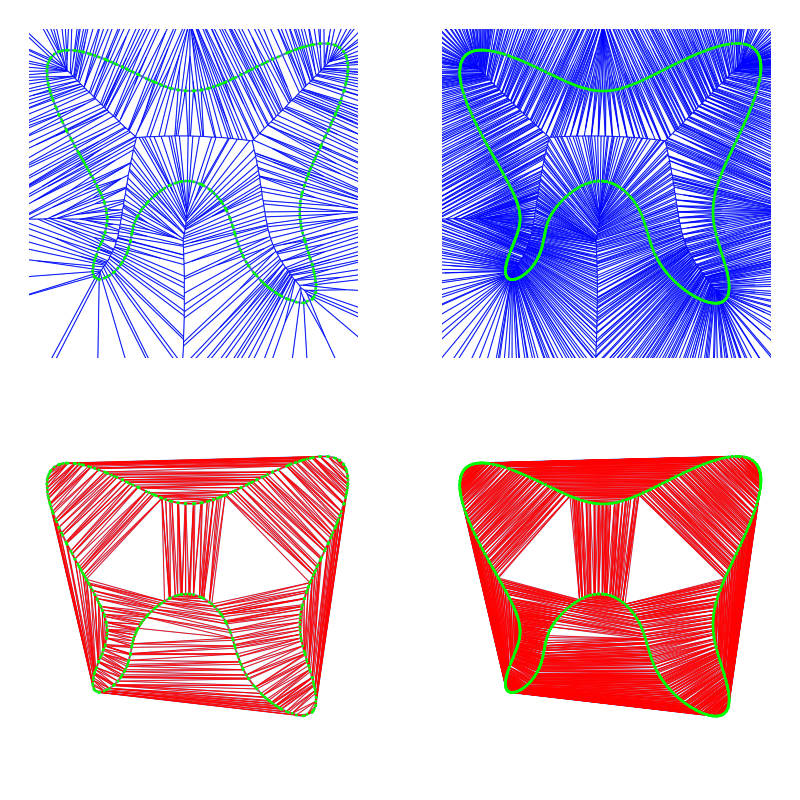

```mathematica
GraphicsGrid[{{MakeVoronoi[f,6],MakeVoronoi[f,40]},{MakeDelaunay[f,6],MakeDelaunay[f,40]}}]
```

## Bottlenecks

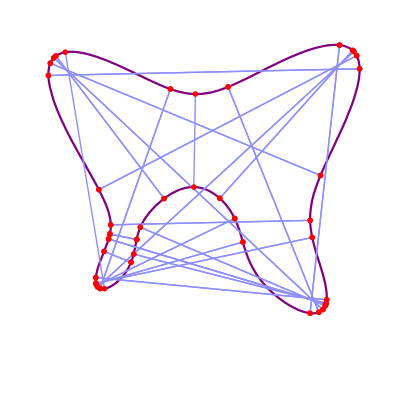

```mathematica
BottleneckPicture[f]
```

```mathematica
smallestbottleneck
```

0.502644

348

0.237002

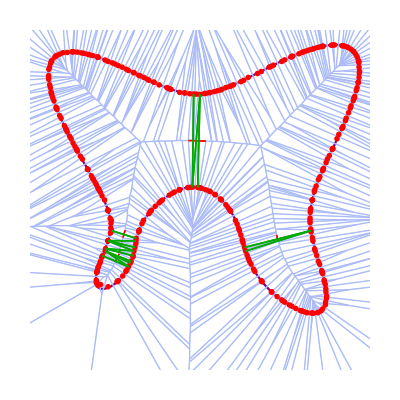

```mathematica
ApproxBottlenecks[f,5]
```

## Critical and maximal curvature

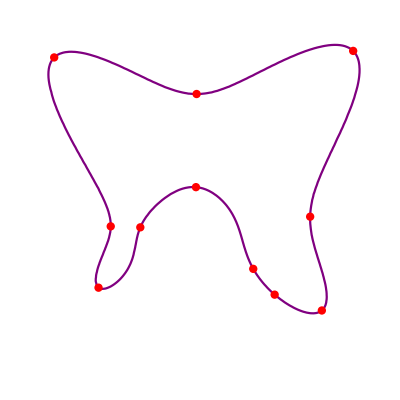

```mathematica
critCurvaturePlot[f]
```

```mathematica
maxlcurvature
```

9.65039

## Reach

```mathematica
reach = Min[maxlcurvature,1/2*smallestbottleneck]
```

0.251322

## Voronoi and Delaunay Lifts

```mathematica
dualpair[ShorePts[f,20]]
```

{-Graphics3D-,-Graphics3D-}

## Medial Axis

348

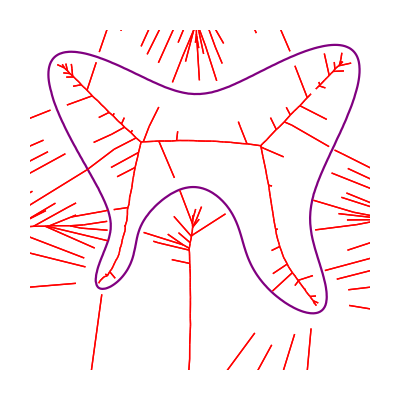

```mathematica
MedialAxis[f,5]
```

2064

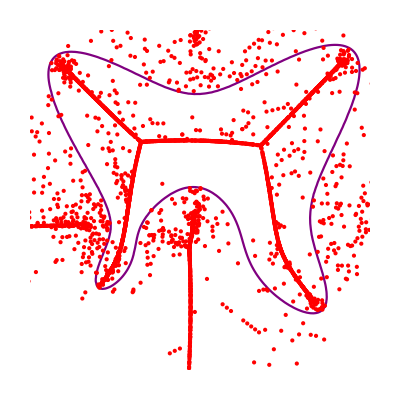

```mathematica
MedialAxisDelaunay[f,5]
```